# Práctica 2.1: Generación de números aleatorios y medida de histogramas

## Apartado 1. Calcular el valor de A para que la distribución (1) esté bien normalizada, teniendo en cuenta que vamos a generar números aleatorios entre -π/2 y π/2.

```mathematica
∫_(-Pi/2)^(Pi/2) A*Cos[x]ⅆx
Solve[%==1,A]
```

2 A

{{A→1/2}}

## Apartado 2. Calcular la probabilidad acumulada F(x) e invertir para aplicarla en el método de la transformada inversa. dz/dx =A*Cos [x]→ z =∫_(-Pi/2)^x 1/2*Cos[x]ⅆx=1/2(Sin[x]+1)⟶x=arcsin(2z-1) con z ϵ [0,1]

## Apartado 3. Generar N = 10^4 números aleatorios y medirlos utilizando Nb = 10 bines. Representarlos junto a la distribución teórica (1) para ver si lo hemos hecho bien.

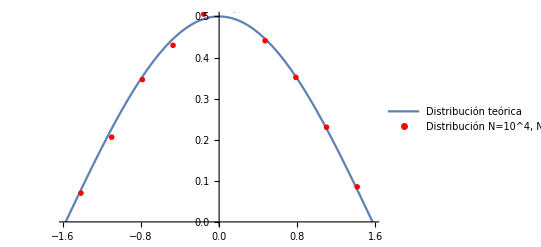

```mathematica
f[x_]=Plot[0.5*Cos[x],{x,-Pi/2,Pi/2}, PlotLegends->{"Distribución f(x)=cos(x)/2"}];
SetDirectory[NotebookDirectory[]];
datosN10E4Nb10=Import["N10E4Nb10.txt","Table"];
grafdatosN10E4Nb10=ListPlot[datosN10E4Nb10,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"Distribución N=10^4, Nb=10"}];
Show[f[x_], grafdatosN10E4Nb10]
```

## Apartado 4. Para estudiar la influencia del número de datos, repetir el proceso para N = 10^2; 10^4 y 10^6, usando en todos los casos Nb = 20 bines. Representar los tres resultados juntos explicando las diferencias.

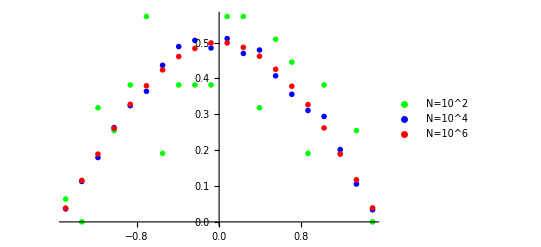

```mathematica
datosN10E2Nb20=Import["N10E2Nb20.txt","Table"];
datosN10E4Nb20=Import["N10E4Nb20.txt","Table"];
datosN10E6Nb20=Import["N10E6Nb20.txt","Table"];

grafdatosN10E2Nb20=ListPlot[datosN10E2Nb20,PlotStyle-> {PointSize[0.01],RGBColor[0,1,0]},PlotRange-> All,PlotLegends->{"N=10^2"}];
grafdatosN10E4Nb20=ListPlot[datosN10E4Nb20,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]},PlotRange-> All,PlotLegends->{"N=10^4"}];
grafdatosN10E6Nb20=ListPlot[datosN10E6Nb20,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"N=10^6"}];

Show[ grafdatosN10E2Nb20, grafdatosN10E4Nb20, grafdatosN10E6Nb20]
```

A medida que aumentamos N la distribución estadística se aproxima a f(x) manteniendo fijo en numero de bines, Nb=20. La distribución que mejor se ajusta es N=10^6 porque tenemos un mayor número de puntos. Lógicamente el peor resultado es para N=10^2.

## Apartado 5. Para estudiar el papel del número de bines, repetir el proceso con N = 10^4 números medidos con Nb = 10; 20 y 100 bines. Representarlos tres resultados juntos y comentar las diferencias.

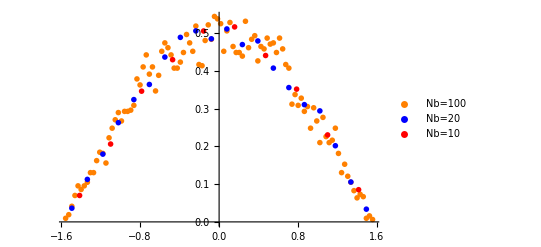

```mathematica
datosN10E4Nb100=Import["N10E4Nb100.txt","Table"];

grafdatosN10E4Nb100=ListPlot[datosN10E4Nb100,PlotStyle-> {PointSize[0.01],RGBColor[1,0.5,0]},PlotRange-> All,PlotLegends->{"Nb=100"}];
grafdatosN10E4Nb20=ListPlot[datosN10E4Nb20,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]},PlotRange-> All,PlotLegends->{"Nb=20"}];

grafdatosN10E4Nb10=ListPlot[datosN10E4Nb10,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"Nb=10"}];

Show[ grafdatosN10E4Nb100, grafdatosN10E4Nb20, grafdatosN10E4Nb10]
```

En este caso a N fijo observamos que a mayor número de bines la dispersión aumenta. Esto es significativamente apreciable para el caso Nb=100 generando una nube de puntos alrededor del máximo.